```mathematica
SetDirectory[NotebookDirectory[]];

IsIndCopula[Copula_]:=(Copula=== "Product");

GetTestName[Copula_,Margs_]:=Module[{n=Length[Margs]},
If[IsIndCopula[Copula], "Independent",ToString[Copula[[1]]]]<>"_"<>StringTrim[ToString[Margs[[1,0]]],"Distribution"]<>"_"<>ToString[n]<>"_dim"
];

PrintResults[EstNames_,AllEsts_,AllStdDevs_,AllTimes_,AllREs_]:=Module[{},
(* Estimates. *)
Print["Estimates:"];
Do[Print["\t* ", EstNames[[e]],": ", AllEsts[[e]]],{e,Length[AllEsts]}];

(* Standard deviations. *)
Print["Standard deviations:"];
Do[Print["\t* ", EstNames[[e]],": ", AllStdDevs[[e]]],{e,Length[AllStdDevs]}];

(* Computation times. *)
Print["Times:"];
Do[Print["\t* ", EstNames[[e]],": ", AllTimes[[e]]],{e,Length[AllTimes]}];

(* Estimated relative errors. *)
Print["Estimated Relative errors:"];
Do[Print["\t* ", EstNames[[e]],": ", AllREs[[e]]],{e,Length[AllREs]}];
];

PlotResults[TestName_,ss_,EstNames_,AllEsts_,AllStdDevs_,AllTimes_,AllREs_]:=Module[{WithS,Colours,EstimatesPlotSmall,EstimatesPlot,StdDevsPlotSmall, StdDevsPlotZoom, SqrtWNRVPlotSmall,SqrtWNRVPlot,CombinedPlot},

WithS[Data_]:=Transpose[{ss,Data}];
Colours=Lookup["DefaultPlotStyle"]@Lookup[Method]@Charting`ResolvePlotTheme[Automatic,Plot];

EstimatesPlotSmall=
ListPlot[Map[WithS,AllEsts],Joined->True,ImageSize-> {250,125},AspectRatio->1/2,PlotStyle->Thickness[0.006],AxesLabel-> {"x","Estimates"}];

EstimatesPlot=
ListPlot[Map[WithS,AllEsts],Joined->True,ImageSize-> {500,125},AspectRatio->0.21,PlotStyle->Thickness[0.006], LabelStyle->{FontSize -> 11}, AxesLabel-> {"x","Estimates"}, PlotRange->{0,0.011}];

StdDevsPlotSmall=
ListPlot[Map[WithS,AllStdDevs],Joined->True,PlotStyle->Thickness[0.012],AxesLabel-> {"x","Standard Deviation"}, LabelStyle->{FontSize -> 11},ImageSize->{250,125},AspectRatio->1/2, PlotRange-> {0,0.07}];

StdDevsPlotZoom=
ListPlot[Map[WithS,AllStdDevs],Joined->True,PlotStyle->Thickness[0.012],AxesLabel-> {"x","Standard Deviation (Zoomed)"}, LabelStyle->{FontSize -> 11}, ImageSize->{250,125},AspectRatio->1/2, PlotRange-> {{200,400},{0,0.007}}];

SqrtWNRVPlotSmall=
ListPlot[Map[WithS,AllREs],Joined->True,ImageSize->{250,125},AspectRatio->1/2,PlotStyle->Thickness[0.012], LabelStyle->{FontSize -> 11}, AxesLabel-> {"x","Sqrt(WNRV)"},PlotRange->{0,0.7}];

SqrtWNRVPlot=
ListPlot[Map[WithS,AllREs],Joined->True,ImageSize-> {500,125},AspectRatio->0.21,PlotStyle->Thickness[0.006], LabelStyle->{FontSize -> 11},AxesLabel-> {"x","Sqrt(WNRV)"}, PlotRange->{0,2}];

CombinedPlot=Legended[Column[{EstimatesPlot,Row[{StdDevsPlotSmall, StdDevsPlotZoom}], SqrtWNRVPlotSmall},Center],Placed[LineLegend[Colours,EstNames,LegendLayout->"Row"],Below]];

Print[TestName<>".pdf"];
Print[CombinedPlot];
Export[TestName<>".pdf",CombinedPlot];
];

PrintAndPlotResults[Copula_,Margs_,R_,ss_,PushoutEsts_,PushoutVars_,PushoutTime_,CondEsts_,CondVars_,CondTime_,AKEsts_,AKVars_,AKTime_]:=Module[{TestName,WithS,Colours,EstNames,AllEsts,AllStdDevs,AllTimes,AllREs,EstimatesPlotSmall,StdDevsPlotSmall,SqrtWNRVPlot,SqrtWNRVPlotSmall,CombinedPlot},

TestName= GetTestName[Copula,Margs];

EstNames={"Sensitivity","CondMC", "AK"};
AllEsts={PushoutEsts,CondEsts,AKEsts};
AllStdDevs=Sqrt@{PushoutVars,CondVars,AKVars};
AllTimes={PushoutTime,CondTime,AKTime};
AllREs=Quiet[Sqrt@{(PushoutTime * (PushoutVars/R)/PushoutEsts^2),(CondTime * (CondVars/R)/CondEsts^2),(AKTime * (AKVars/R)/AKEsts^2)},{Power::infy,Infinity::indet}];

PlotResults[TestName,ss,EstNames,AllEsts,AllStdDevs,AllTimes,AllREs];

Print[TestName," done"];
];
```

Clayton_Weibull_10_dim.pdf

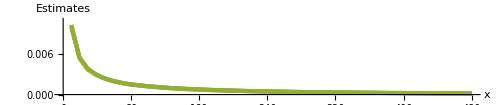
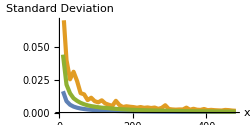
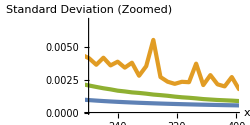
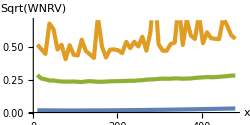

Clayton_Weibull_10_dim done

```mathematica
(* Test 2: {"Clayton",1/5},WeibullDistribution[3/10,1] *)
Copula={"Clayton",1/5};
Margs=Table[WeibullDistribution[3/10,1],{i,10}];
R=10^5;
ss={9.605970638829037,19.211941277658074,28.817911916487112,38.42388255531615,48.02985319414518,57.635823832974225,67.24179447180326,76.8477651106323,86.45373574946133,96.05970638829037,105.6656770271194,115.27164766594845,124.87761830477749,134.48358894360652,144.08955958243556,153.6955302212646,163.30150086009363,172.90747149892266,182.5134421377517,192.11941277658073,201.72538341540977,211.3313540542388,220.93732469306784,230.5432953318969,240.14926597072593,249.75523660955497,259.361207248384,268.96717788721304,278.5731485260421,288.1791191648711,297.78508980370015,307.3910604425292,316.9970310813582,326.60300172018725,336.2089723590163,345.8149429978453,355.42091363667436,365.0268842755034,374.6328549143324,384.23882555316146,393.8447961919905,403.45076683081953,413.05673746964857,422.6627081084776,432.26867874730664,441.8746493861357,451.4806200249647,461.0865906637938,470.69256130262283,480.29853194145187};
PushoutEsts={0.009981381702133708,0.005403281483544952,0.0037717135624351326,0.002920257099981706,0.002393559317774508,0.002031159925621343,0.001764533175499865,0.0015602076955454813,0.0013971950910249746,0.0012621770036571362,0.0011490649856636642,0.0010538472651175886,0.0009720946712978432,0.0009010124361782086,0.0008381981046678567,0.0007822059101121423,0.0007319309058780936,0.0006868926084731499,0.000645870609905852,0.0006084653640243074,0.0005745421463369868,0.0005437974702225185,0.0005153870145074684,0.000488887423449342,0.00046453602832281207,0.0004411919443569072,0.0004197548823043694,0.0004002184764521294,0.00038107029812528174,0.00036360895945478696,0.0003475121708690361,0.0003322879414960273,0.0003178302222992239,0.00030460804427501524,0.00029181964707598407,0.0002795519973451412,0.00026783502025469735,0.00025662797928650003,0.00024633389761151566,0.00023707942352945227,0.00022723279066562475,0.00021816622202530932,0.00020960109626440515,0.00020131845587848874,0.00019377714549978308,0.00018690727021827784,0.00018009968937533598,0.0001736491108255397,0.00016706099516562822,0.00016110026503277748};
CondEsts={0.01010775151513915,0.005362826088401746,0.0036691223613275837,0.0029716914375746946,0.002450877293743658,0.0019917388837115938,0.0017396588930624764,0.0015108556305131998,0.0014232895733676323,0.0012739438579481362,0.0011585927366068972,0.0010867521442487794,0.0009516373451216154,0.0008630310684509372,0.0007856462277167207,0.0007939734677492726,0.0007363358544875797,0.0006481956012052821,0.000645319066289593,0.0005921345212787574,0.0005649730031458648,0.0005214622625268898,0.0005027066600082331,0.0004742624589023761,0.0004656290848491296,0.00043987848939838146,0.0004259742367375618,0.0003859046798910093,0.00037258321636731947,0.0003703899097852286,0.0003360267540070513,0.00032279870079660256,0.0003009932473926999,0.0002906900387941052,0.0002812942919862715,0.00029086372194588495,0.0002635183109913308,0.00026160163428073935,0.00023743933709611376,0.00023004314925889762,0.00023618395782856023,0.00021933815655597,0.00021438122057865496,0.0002038236653161855,0.00018753763789519087,0.00017675034003786366,0.00017766942460008985,0.00017785391060991137,0.00016352038255111818,0.00015298216394660837};
AKEsts={0.0102735557438549,0.005473105562223495,0.0038486264831692637,0.0029730295092675867,0.002427083827617184,0.002054171998731667,0.001771264355085969,0.0015483038287342538,0.0013785810002466337,0.001259018596490161,0.001157002819384072,0.001059217535761275,0.0009893516985510387,0.0009171837200261465,0.000854899680541717,0.0007955938754297732,0.000739632651231367,0.0006906193168162832,0.0006433126061741241,0.0006045355439139606,0.0005731601338767118,0.0005403347580787019,0.0005111371442236217,0.00048489421574095194,0.00045869252296306485,0.0004364838601837716,0.00041485208370846904,0.0003965803257047412,0.0003791664712034558,0.0003603171762047603,0.000344069427911358,0.00032870373393811716,0.0003136292133397783,0.00029960014788031977,0.00028800264073308387,0.00027652427456704943,0.00026476156033279787,0.0002546434416425815,0.0002447211137474837,0.00023529924498149544,0.00022662415406282527,0.00021724664266329106,0.00020955760352192279,0.00020099620823338764,0.00019333445499177793,0.00018609440356281143,0.00017908920778615534,0.00017235201134811217,0.00016639543596721787,0.0001599425825078789};

PushoutVars={0.016136129597538938,0.008624467077880008,0.005920584083894197,0.004511632917510368,0.003648663656352494,0.0030645055670124126,0.002642281224069751,0.0023236974856319223,0.0020749784815353254,0.0018757768763537216,0.001712266578633806,0.0015767741273051991,0.0014612533182896156,0.001362463307541997,0.0012774642830698252,0.001203508967655865,0.0011385667313273768,0.0010809790947427461,0.0010298085505467101,0.0009841116292146812,0.0009425711758720408,0.0009048503636356248,0.0008705627496295468,0.0008394894462106242,0.0008109786724749952,0.0007854299862162995,0.0007615477745783808,0.0007390128379254664,0.0007190572701986344,0.0006999485028942634,0.0006818325535396658,0.0006649250905960271,0.0006492796858462609,0.0006341545133104401,0.0006201513002801965,0.000607007775646547,0.0005946743802435214,0.0005830761701444547,0.0005717636984104759,0.000560547617204829,0.0005508018494109239,0.0005412223717820014,0.000532022254675957,0.0005231832612384636,0.0005146861092392091,0.0005059164869426775,0.0004978159726225252,0.0004898851228786256,0.00048239072570467097,0.00047503627116659625}^2;
CondVars={0.0803370043709051,0.0397694894019261,0.025209000579983668,0.030941557067242866,0.02391526746860577,0.014708548556841693,0.01379269490472114,0.00942710796044234,0.011223010919002612,0.008613456627535696,0.0077344541063520565,0.009265491618531853,0.006868887608585658,0.005883600616658664,0.005022957452105352,0.008888796343394107,0.005683593624013732,0.00417924375798689,0.004744581951583389,0.004377846237430172,0.004114412568709887,0.0036262152664417514,0.004158750482309213,0.003574859529807438,0.0038586927786887605,0.003405774752869685,0.0037800594691964388,0.002790949209624329,0.003517448150421576,0.005512421570292733,0.0026924528671713483,0.0023385865851683753,0.0021766586261951167,0.0023322815139949693,0.002300584162460531,0.003709447027388385,0.0020834288485038857,0.0028404317939867522,0.0021386768270888028,0.0019832037917176843,0.002693095780455178,0.0017788259973763646,0.0020136705721065045,0.0017747918865720132,0.0016179460869630658,0.0015191828830703063,0.0019687587835905355,0.0018059657348706247,0.0014781782846924412,0.0013208639579463833}^2;
AKVars={0.043934892234780774,0.021199884939359707,0.01458890001271332,0.010835674565938034,0.008864236002150888,0.0073537718711795385,0.006271958862280896,0.005461203982304155,0.004862144315024697,0.0044578432558697685,0.004058563502242715,0.003683839907961624,0.003512283951724953,0.003280311237532096,0.00303016358051126,0.002784458980496003,0.002598238960540382,0.0024408086356463156,0.0022901151332630587,0.002157894664676868,0.002048667823837431,0.0019422924813692086,0.0018412208922857353,0.0017593905505171007,0.001658336608106699,0.0016002160930739296,0.0015294606304216384,0.0014874519645941442,0.0014311306412879555,0.0013638145095011486,0.001320098074158982,0.0012712604421846966,0.0012076424581809323,0.001155997653707323,0.0011206354630153275,0.0010746266069576755,0.0010209021049861881,0.0009863627873193531,0.0009516236267750785,0.0009276334022338103,0.0009028359326113998,0.0008710575173330022,0.0008465569274268618,0.0008087459037647687,0.0007794812267121075,0.0007579276458112641,0.0007368785544902549,0.0007145642789647677,0.0007012630733364433,0.0006747126250217232}^2;

PushoutTime=10.9765;
CondTime=420.092;
AKTime=442.81;

PrintAndPlotResults[Copula,Margs,R,ss,PushoutEsts,PushoutVars,PushoutTime,CondEsts,CondVars,CondTime,AKEsts,AKVars,AKTime]
```